```mathematica
filesAR=FileNames["/home/carla/GDC/CONF/PHI/GDC_Conf_AR_PHI_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/CONF/PHI/GDC_Conf_BR_PHI_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojCHEVBKAR=confAR[[All,1]][[All,1]]
dojCHAR=confAR[[All,2]][[All,3]]
dojEVBKAR=confAR[[All,3]][[All,3]]

dojCHEVBKBR=confBR[[All,1]][[All,1]]
dojCHBR=confBR[[All,2]][[All,3]]
dojEVBKBR=confBR[[All,3]][[All,3]]
```

{0.000793021,0.00505051,0.0333333,0.0222222,0.0133333,0.04,1.}

{0.000277936,0.000265757,0.0010752,0.000612063,0.000342354,0.000338286,0.000435964}

{0.000038195,8.71422×10^-7,3.21816×10^-8,3.23528×10^-9,5.48943×10^-10,2.68221×10^-11,9.9865×10^-14}

{0.000793021,0.00505051,0.0231729,0.0133333,0.0133333,0.0416667}

{0.000265757,0.000279347,0.000612063,0.000342354,0.000338286,0.000335743}

{0.0000221993,1.18943×10^-6,4.83998×10^-8,2.74471×10^-9,8.04663×10^-11,2.39676×10^-12}

```mathematica
(*sList={"S0","S1","S2","S3","S4","S5","S6","S7","S8"};
dojP=Labeled[#[[1]],#[[2]]]&/@Map[{doj[[#]],sList[[#]]}&,ran]*)

sList={2,3,4,5,6,7,8};
sList2={2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojAAR={#[[2]],#[[1]]}&/@Map[{N[dojCHAR[[#]]/dojCHEVBKAR[[#]]],sList[[#]]}&,ran]
dojABR={#[[2]],#[[1]]}&/@Map[{N[dojCHBR[[#]]/dojCHEVBKBR[[#]]],sList2[[#]]}&,ran2]
dojPCHAR={#[[2]],#[[1]]}&/@Map[{dojCHAR[[#]],sList[[#]]}&,ran]
dojPCHBR={#[[2]],#[[1]]}&/@Map[{dojCHBR[[#]],sList2[[#]]}&,ran2]
dojPEVBKAR={#[[2]],#[[1]]}&/@Map[{dojEVBKAR[[#]],sList[[#]]}&,ran]
dojPEVBKBR={#[[2]],#[[1]]}&/@Map[{dojEVBKBR[[#]],sList2[[#]]}&,ran2]
```

{{2,0.350477},{3,0.0526199},{4,0.032256},{5,0.0275429},{6,0.0256765},{7,0.00845715},{8,0.000435964}}

{{2.5,0.33512},{3.5,0.0553106},{4.5,0.0264129},{5.5,0.0256765},{6.5,0.0253715},{7.5,0.00805784}}

{{2,0.000277936},{3,0.000265757},{4,0.0010752},{5,0.000612063},{6,0.000342354},{7,0.000338286},{8,0.000435964}}

{{2.5,0.000265757},{3.5,0.000279347},{4.5,0.000612063},{5.5,0.000342354},{6.5,0.000338286},{7.5,0.000335743}}

{{2,0.000038195},{3,8.71422×10^-7},{4,3.21816×10^-8},{5,3.23528×10^-9},{6,5.48943×10^-10},{7,2.68221×10^-11},{8,9.9865×10^-14}}

{{2.5,0.0000221993},{3.5,1.18943×10^-6},{4.5,4.83998×10^-8},{5.5,2.74471×10^-9},{6.5,8.04663×10^-11},{7.5,2.39676×10^-12}}

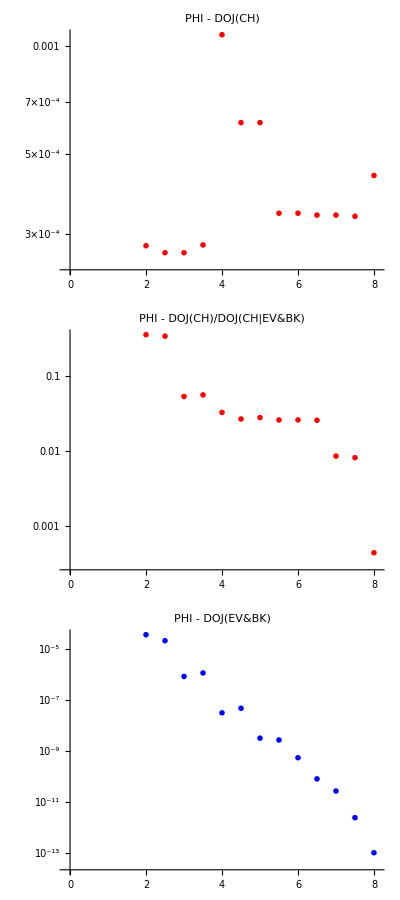

```mathematica
aPlot=ListLogPlot[{Union[dojAAR,dojABR]},  PlotLabel->"PHI - DOJ(CH)/DOJ(CH|EV&BK)", PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red}, PlotRange->All, PlotMarkers->{{"A",12}},ImageSize->400];
chPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR]}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"PHI - DOJ(CH)", PlotMarkers->{{"C",12}},ImageSize->400];
evbkPlot=ListLogPlot[{Union[dojPEVBKAR,dojPEVBKBR]},PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Blue}, PlotRange->All, PlotLabel->"PHI - DOJ(EV&BK)", PlotMarkers->{{"E",12}},ImageSize->400];
allPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR], Union[dojPEVBKAR,dojPEVBKBR]}, PlotLegends->{"DOJ(CH)","DOJ(EV&BK)"}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red, Blue}, PlotRange->All, PlotLabel->"PHI - DOJ(CH),DOJ(EV&BK)", PlotMarkers->{{"C",12},{"E",12}},ImageSize->400];
plotsOut=Column[{chPlot,aPlot,evbkPlot}, ItemSize->35, Alignment->Center]
```

```mathematica
SetDirectory["/home/carla/GDC/CONF/PHI/"];
Export["PHI_CH_EVBK.jpeg",plotsOut,ImageResolution->200]
Put[Union[dojPCHAR,dojPCHBR],"PHI_Z_APP.txt"]
Put[Union[dojAAR,dojABR],"PHI_F_APP.txt"]
```

PHI_CH_EVBK.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.026},  PlotLabel->"PHI - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["PHI_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```